# Software Paper

```mathematica
(*Set the path for the experiments*)
USER=3;
return=If[USER==1,SetDirectory["/Users/sanchez.hmsc/odrive/MGDrivE_Experiments/MCR"],1];
return=If[USER==2,SetDirectory["/Volumes/Pusheen/xjego-khuq3/MCR"],1];
return=If[USER==3,SetDirectory["/Users/sanchez.hmsc/Desktop/SoftwarePaper_OUT"],1];
If[return==1,Print["PATH ERROR"],Print["Path setup correctly"]];
(*Set a name for the outputs and define experiment's ranges*)
experimentName="SD";
{releasesStart,releasesInterval,timeRange}={25,7,{1,365*3-1}};
(*Select the aggregation indices for genotypes*)
artificialColor=CreateColorBlend[3,"LakeColors",{20,15}];
genotypesGroups={
{{1,1,2,3,4},"W"},
{{2,5,5,6,7},"H"},
{{3,6,7,8,8},"R"}(*,
{{4,7,9,10,10},"B"}*)
};
(*Define genotypes colors*)
originalColorsValues={
{0,100,70,0},
{70,50,0,0},
{50,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
Transpose[{rgbColors,genotypesGroups[[All,2]]}]//Grid
```

Path setup correctly

RGBColor[1., 0., 0.30000000000000004] | W
RGBColor[0.30000000000000004, 0.5, 1.] | H
RGBColor[0.5, 0., 1.] | R

## 0) Functions

Plots

```mathematica
CreateColorBlend[genotypesNumber_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=ColorData[colorSchemeName][#]&/@Range[0,1,1/genotypesNumber]
]
PlotLineDynamics[aggregatedGroupData_,genotypeIndex_,rgbaColors_,{opacity_,thickness_},plotRange_]:=ListLinePlot[
aggregatedGroupData[[All,All,genotypeIndex]]
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->plotRange
,PlotRangePadding->0
,PlotStyle->Directive[rgbaColors[[genotypeIndex]],Thickness[thickness],Opacity[opacity]]
]
GenerateMatrixPlotsNonNormalized[aggregatedGroupData_,timeRange_,maxesMax_,releaseTimes_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@releaseTimes,
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1/maxesMax]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
GenerateStreamChart[counts_]:=BarChart[counts//Transpose
,PerformanceGoal->"Speed"
,AspectRatio->1/4
,Axes->False
,FrameLabel->(Style[#,50]&/@{"Time","Genotype Breakdown"})
,BarSpacing->{0,0}
,ChartLayout->"Stacked"
,ChartStyle->(Directive[Opacity[.6],Lighter[#,0],EdgeForm[None]]&/@rgbColors)
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicks->{{None,Range[0,10000,100]},{Range[0,1.5*counts//Flatten//Max,250],None}}
,FrameTicksStyle->{
{Directive[Black,25],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,25]}
}
,GridLines->{Range[0,50000,100],Range[0,1.5*counts//Flatten//Max,100]}
,GridLinesStyle->Directive[Gray,Dashed]
,ImagePadding->Automatic
,ImageSize->2000
,PlotRangePadding->{0,0}
,PlotRange->{{timeRange[[1]],All},{0,1.1*Max[Total/@Transpose[counts]]}}
,Epilog->Flatten[{Thickness[.001],Dashed,(Line[{{#,0},{#,1.1*Max[Total/@Transpose[counts]]}}]&/@{releaseTimes[[1]]})}]
]
GenerateMatrixPlotsSplits[matrixPlots_]:=GraphicsGrid[Prepend[
Transpose[{Show[#,FrameTicks->None]&/@matrixPlots}],
{Show[matrixPlots,FrameTicks->None]}
]]
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateMatrixPlots[aggregatedGroupData_,timeRange_,maxesMax_,rgbaColors_]:=Module[{matrixPlots,genotypeA},
aspectRatio=7.5;
matrixPlots=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeA=genotypeA/maxesMax;
MatrixPlot[genotypeA
,AspectRatio->1/aspectRatio
,Frame->True
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameLabel->{
{Style["Time",.001],None},
{None,Style[Rotate["House ID",π],.001]}
}
,ImageSize->2000
,FrameTicks->{
{
Automatic,
Automatic
(*{#,#,{1,0},Directive[Thickness[.00025],Dashed]}&/@Accumulate[clustersLengths][[1;;(Length[clusters]-1)]]*)
},
{
{#,#,{1/aspectRatio,0},Directive[Thickness[.002],Dashed]}&/@{releaseTimes[[1]]},
Automatic
}
}
,FrameTicksStyle->{
{Directive[Black,40],Directive[Black,.00001]},
{Directive[Black,.00001],Directive[Black,40]}
}
,PlotRangePadding->None
,ColorFunction->(Blend[{rgbaColors[[i,1]],rgbaColors[[i,2]]},1.1*#1]&)
,ColorFunctionScaling->False
(*,Epilog->Flatten[{Thick,Line[{{0,0},{timeRange[[2]]-1,850}}]}]*)
]
,{i,1,genotypesGroups//Length}];
matrixPlots
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
```

Data

```mathematica
AggregateByGenotype[rawDataTotal_,genotypesGroups_]:=Module[{aggregatedData,outputTotals,totals,transposedTotals},
outputTotals=Table[
aggregatedData=#[[All,genotypesGroups[[i,1]]]]&/@rawDataTotal;
totals=Map[Total,aggregatedData,{2}];
totals
,{i,1,genotypesGroups//Length}];
transposedTotals=Transpose/@Transpose[outputTotals];
transposedTotals
]

GetMaxPopulation[aggregatedGroupData_,genotypesGroups_,timeRange_]:=Module[{i,maxes,genotypeA,genotypeAtemp,maxesMax},
i=1;
maxes=Table[
genotypeA=(#[[timeRange[[1]];;timeRange[[2]],i]]&)/@aggregatedGroupData;
genotypeAtemp=Max[#]&/@genotypeA
,{i,1,genotypesGroups//Length}];
maxesMax=Max/@Transpose[maxes];
maxesMax
]

FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
CalculateCounts[aggregatedGroupData_,genotypesGroups_]:=Module[{genotypeTemp,genotypeTotal},
Table[
genotypeTemp=aggregatedGroupData[[All,All,i]];
genotypeTotal=Total/@Transpose[genotypeTemp];
genotypeTotal
,{i,1,Length[genotypesGroups]}]
]
ImportExperimentRawData[experimentString_]:=Module[{experimentFolders,releaseTimes,rawDataExperiments,cellFolder,sweepID,filenames,rawData,rawDataTotal,genotypes,null,drive,releases,size,filenamesFemale,filenamesMale,rawDataMale,rawDataFemale},
experimentFolders=FileNames[experimentString<>"/0*",Directory[]];
rawDataExperiments=Table[
cellFolder=experimentFolders[[i]];
sweepID={null,drive,releases,size}=ToExpression/@(StringSplit[StringSplit[experimentString,{"/"}],"_"]//Last);
filenames={filenamesMale,filenamesFemale}=FileNames[#,cellFolder]&/@{"ADM_*","AF1_*"};(*CHANGE TO AF1*)
rawData={rawDataMale,rawDataFemale}=ParallelMap[Import[#][[2;;All,2;;All]]&,#]&/@filenames;
rawDataTotal=rawDataMale+rawDataFemale;
genotypes=Import[filenamesMale[[1]]][[1,2;;All]];
rawDataTotal
,{i,1,experimentFolders//Length}];
{Range[genotypes//Length],genotypes}//Grid[#,Frame->All]&;
{rawDataExperiments,genotypes}
]
CalculateGenotypesGroups[genotypes_]:=Module[{alleles,splits,genotypesGroups},
alleles=Flatten[StringPartition[#,1]&/@genotypes]//DeleteDuplicates;
splits=StringPartition[#,1]&/@genotypes;
genotypesGroups={
Flatten/@(Table[ConstantArray[i,Count[splits[[i]],#]]&/@alleles,{i,1,splits//Length}]//Transpose),
alleles
}//Transpose
]
```

## 1) Population Aggregation

Deterministic

{0.0075,1,{{0,All},{0,4750}}}

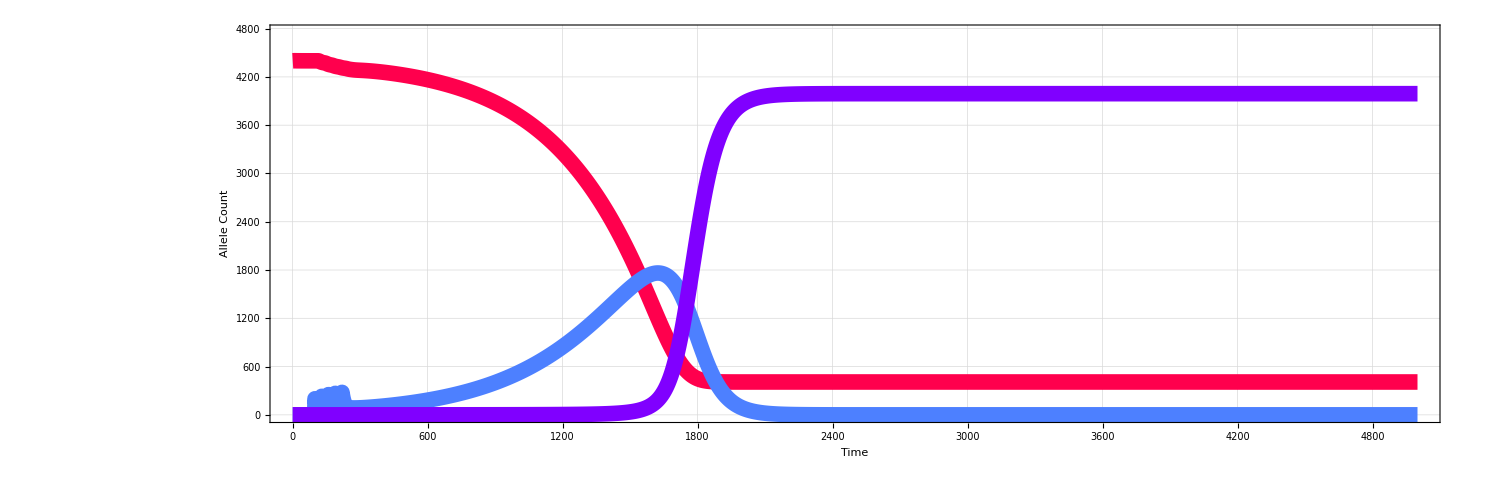

```mathematica
repDetPath="/Suppression/Deterministic/0001/";
(**)
filenames={fileNamesMale,filenamesFemale}={FileNames["ADM*",Directory[]<>repDetPath],FileNames["AF1_Aggregate*",Directory[]<>repDetPath]};
{dataRawMale,dataRawFemale}=ParallelTable[Import[#]&/@i,{i,filenames}];
{dataMale,dataFemale}={dataRawMale[[All,2;;All,2;;All]],dataRawFemale[[All,2;;All,2;;All]]};
dataTotal=(dataMale+dataFemale);
genotypes=dataRawMale[[1,1,2;;All]];
(**)
aggregatedData=AggregateByGenotype[dataTotal,genotypesGroups];
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
{thickness,opacity,range}={.0075,1,{{0,All},{0,4750}}}
(**)
deterministicListPlot=ListLinePlot[
(*(Accumulate/@*)(Total[aggregatedData])//Transpose
,AspectRatio->1/3
,Filling->Append[{1->Bottom},((#+1)->{#})&/@Range[1,(aggregatedData[[1,1]]//Length)-1]]
,FillingStyle->Directive[Opacity[0]]
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->range
,PlotRangePadding->0
,PlotStyle->(Directive[#,Thickness[thickness],Opacity[opacity]]&/@rgbaColors)
]
```

Stochastic

```mathematica
iterations=Table[
repDetPath="/Suppression/Stochastic/"<>StringPadLeft[ToString[i],4,"0"]<>"/";
filenames={fileNamesMale,filenamesFemale}={FileNames["ADM*",Directory[]<>repDetPath],FileNames["AF1_Aggregate*",Directory[]<>repDetPath]};
{dataRawMale,dataRawFemale}=ParallelTable[Import[#]&/@i,{i,filenames}];
{dataMale,dataFemale}={dataRawMale[[All,2;;All,3;;All]],dataRawFemale[[All,2;;All,3;;All]]};
dataTotal=(dataMale+dataFemale);
genotypes=dataRawMale[[1,1,2;;All]];
(**)
aggregatedData=AggregateByGenotype[dataTotal,genotypesGroups];
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
{thickness,opacity,range}={.00005,.5,{{0,All},{0,4750}}};
(**)
ListLinePlot[
(*(Accumulate/@*)(Total[aggregatedData])//Transpose
,AspectRatio->1/3
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->range
,PlotRangePadding->0
,PlotStyle->(Directive[#,Thickness[thickness],Opacity[opacity]]&/@rgbaColors)
]
,{i,1,100}];
Show[iterations];
```

```mathematica
iterationsData=Table[
repDetPath="/Suppression/Stochastic/"<>StringPadLeft[ToString[i],4,"0"]<>"/";
filenames={fileNamesMale,filenamesFemale}={FileNames["ADM*",Directory[]<>repDetPath],FileNames["AF1_Aggregate*",Directory[]<>repDetPath]};
{dataRawMale,dataRawFemale}=ParallelTable[Import[#]&/@i,{i,filenames}];
{dataMale,dataFemale}={dataRawMale[[All,2;;All,3;;All]],dataRawFemale[[All,2;;All,3;;All]]};
dataTotal=(dataMale+dataFemale);
genotypes=dataRawMale[[1,1,2;;All]];
(**)
aggregatedData=AggregateByGenotype[dataTotal,genotypesGroups];
(*(Accumulate/@*)(Total[aggregatedData])//Transpose
,{i,1,100}];
```

```mathematica
{thicknessTwo,opacityTwo}={.004,.5};
medianPopulations=Table[
Mean/@((Transpose/@(Transpose[iterationsData]))[[i]])
,{i,1,3}];
medianPlot=ListLinePlot[
medianPopulations
,AspectRatio->1/3
,Filling->Append[{1->Bottom},((#+1)->{#})&/@Range[1,(aggregatedData[[1,1]]//Length)-1]]
,FillingStyle->Directive[Opacity[0]]
,Frame->True
,FrameLabel->(Style[#,50]&/@{"Time","Allele Count"})
,FrameTicksStyle->20
,FrameStyle->Thick
,GridLines->Automatic
,GridLinesStyle->Directive[Gray,Thin]
,ImageSize->1500
,InterpolationOrder->1
,PlotRange->range
,PlotRangePadding->0
,PlotStyle->(Directive[#,Thickness[thicknessTwo],Dashing[.0075],Opacity[opacityTwo]]&/@rgbaColors)
];
Show[iterations,medianPlot];
```

```mathematica
Show[
Show[medianPlot,iterations,AspectRatio->1/5],
Show[deterministicListPlot,AspectRatio->1/5]
,FrameStyle->Directive[Black,Thickness[.002]]
,FrameTicksStyle->Directive[Black,40]
]
Export["dynamicsPlot.png",%,ImageSize->3000]
```

-Graphics-

dynamicsPlot.png

## 2) Landscape Flow

Deterministic

```mathematica
repDetPath="/Replacement/Deterministic/0001/";
(**)
filenames={fileNamesMale,filenamesFemale}={FileNames["ADM*",Directory[]<>repDetPath],FileNames["AF1_Aggregate*",Directory[]<>repDetPath]};
{dataRawMale,dataRawFemale}=ParallelTable[Import[#]&/@i,{i,filenames}];
{dataMale,dataFemale}={dataRawMale[[All,2;;All,2;;All]],dataRawFemale[[All,2;;All,2;;All]]};
dataTotal=(dataMale+dataFemale);
genotypes=dataRawMale[[1,1,2;;All]];
(**)
aggregatedData=AggregateByGenotype[dataTotal,genotypesGroups];
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
{thickness,opacity,range}={.0075,1,{{0,All},{0,4750}}}
```

{0.0075,1,{{0,All},{0,4750}}}

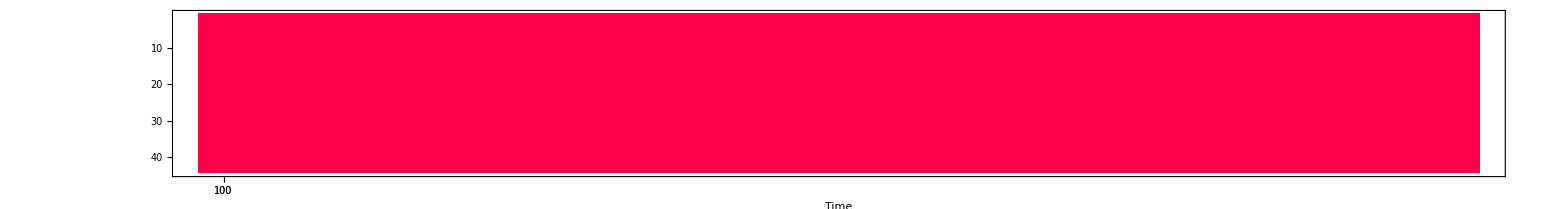
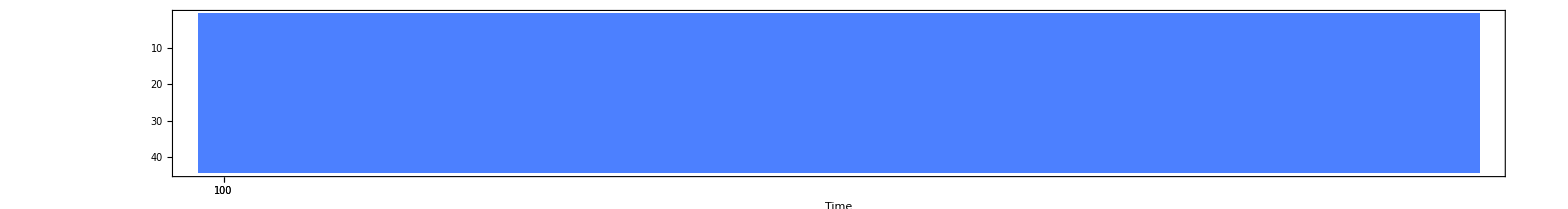
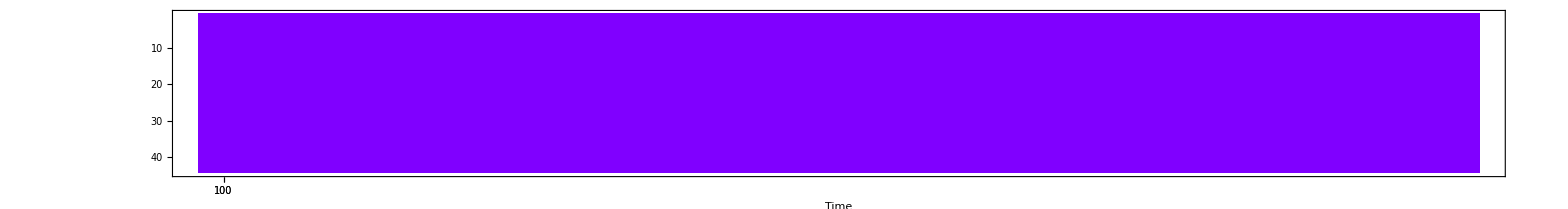

{R001.png,R002.png,R003.png}

```mathematica
flows=GenerateMatrixPlotsNonNormalized[aggregatedData,{1,aggregatedData[[1]]//Length},(aggregatedData//Flatten//Max)*.5,{100,100}]
Table[
Export["R"<>StringPadLeft[ToString[i],3,"0"]<>".png",flows[[i]],ImageSize->3000]
,{i,1,3}]
```

Stochastic

```mathematica
iterationsData=Table[
repDetPath="/Suppression/Stochastic/"<>StringPadLeft[ToString[i],4,"0"]<>"/";
filenames={fileNamesMale,filenamesFemale}={FileNames["ADM*",Directory[]<>repDetPath],FileNames["AF1_Aggregate*",Directory[]<>repDetPath]};
{dataRawMale,dataRawFemale}=ParallelTable[Import[#]&/@i,{i,filenames}];
{dataMale,dataFemale}={dataRawMale[[All,2;;All,3;;All]],dataRawFemale[[All,2;;All,3;;All]]};
dataTotal=(dataMale+dataFemale);
genotypes=dataRawMale[[1,1,2;;All]];
(**)
aggregatedData=AggregateByGenotype[dataTotal,genotypesGroups];
aggregatedData
,{i,1,100}];
```

```mathematica
{thicknessTwo,opacityTwo}={.004,.5};
medianPopulations=ParallelTable[
Mean/@((Transpose/@(Transpose[iterationsData]))[[i]])
,{i,1,44}];
```

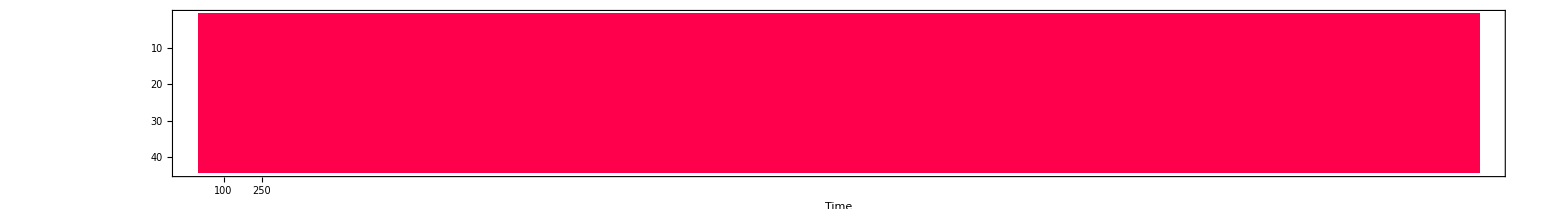
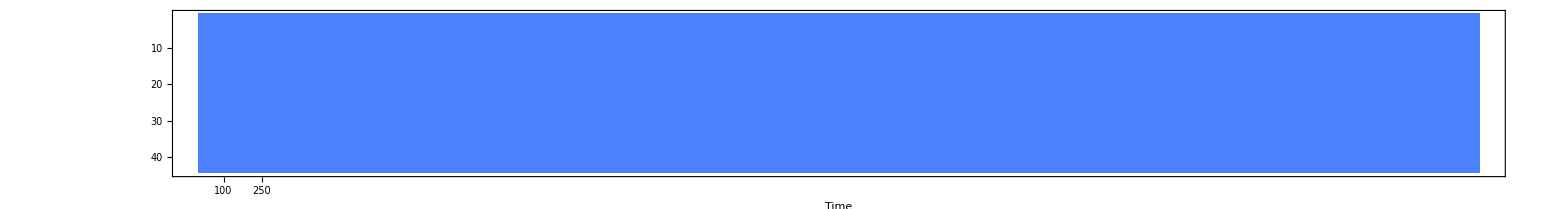
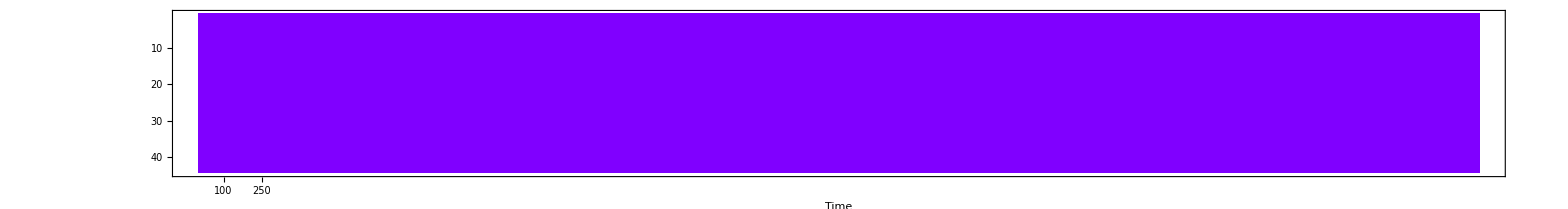

{S001.png,S002.png,S003.png}

```mathematica
flows=GenerateMatrixPlotsNonNormalized[medianPopulations,{1,aggregatedData[[1]]//Length},(aggregatedData//Flatten//Max)*.5,{100,250}]
Table[
Export["S"<>StringPadLeft[ToString[i],3,"0"]<>".png",flows[[i]],ImageSize->3000]
,{i,1,3}]
```